```mathematica
(*Mathematica*)
```

```mathematica
Clear[e,c,v]
```

```mathematica
(*{e,c} 17d Fuchsian Identity*)
```

```mathematica
(9/8)*Apply[Times,Join[Table[e,{i,9}],Table[c,{i,8}]]]
```

(9 c^8 e^9)/8

```mathematica
Reduce[(9 c^8 e^9)/8-1==0,{e,c}]
```

e≠0&&(c==-((-1/3)^(1/4) 2^(3/8))/e^(9/8)||c==((-1/3)^(1/4) 2^(3/8))/e^(9/8)||c==-2^(3/8)/(3^(1/4) e^(9/8))||c==-(ⅈ 2^(3/8))/(3^(1/4) e^(9/8))||c==(ⅈ 2^(3/8))/(3^(1/4) e^(9/8))||c==2^(3/8)/(3^(1/4) e^(9/8))||c==-((-1)^(3/4) 2^(3/8))/(3^(1/4) e^(9/8))||c==((-1)^(3/4) 2^(3/8))/(3^(1/4) e^(9/8)))

```mathematica
e≠0&&(c==-((-1/3)^(1/4) 2^(3/8))/e^(9/8)||c==((-1/3)^(1/4) 2^(3/8))/e^(9/8)||c==-2^(3/8)/(3^(1/4) e^(9/8))||c==-(ⅈ 2^(3/8))/(3^(1/4) e^(9/8))||c==(ⅈ 2^(3/8))/(3^(1/4) e^(9/8))||c==2^(3/8)/(3^(1/4) e^(9/8))||c==-((-1)^(3/4) 2^(3/8))/(3^(1/4) e^(9/8))||c==((-1)^(3/4) 2^(3/8))/(3^(1/4) e^(9/8)))/.e->4.80325*10^(-10)
```

c==-2.12014×10^10-2.12014×10^10 ⅈ||c==2.12014×10^10+2.12014×10^10 ⅈ||c==-2.99833×10^10||c==0.-2.99833×10^10 ⅈ||c==0.+2.99833×10^10 ⅈ||c==2.99833×10^10||c==2.12014×10^10-2.12014×10^10 ⅈ||c==-2.12014×10^10+2.12014×10^10 ⅈ

```mathematica
v=Abs[{e,c}]/.NSolve[(9 c^8 e^9)/8-1==0,{e,c}]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(92291 c)/87992-(121001 e)/175984 == 1.

{{2.09088,0.42977},{2.09088,0.42977},{1.97756,0.457571},{1.97756,0.457571},{1.75195,0.524377},{1.75195,0.524377},{0.720191,1.42553},{0.736501,1.39007},{0.736501,1.39007},{0.790387,1.28391},{0.790387,1.28391},{1.43055,0.658667},{1.43055,0.658667},{0.900405,1.10883},{0.900405,1.10883},{1.10756,0.878402},{1.10756,0.878402}}

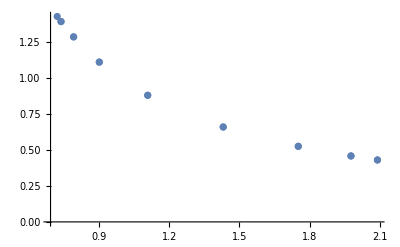

```mathematica
ListPlot[v]
```

```mathematica
w={2*e,2*c,1-e^2-c^2}/(1+e^2+c^2)/.NSolve[(9 c^8 e^9)/8-1==0,{e,c}]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(92291 c)/87992-(121001 e)/175984 == 1.

{{-0.754771+0.053521 ⅈ,0.15421+0.0202098 ⅈ,-0.642788-0.0579966 ⅈ},{-0.754771-0.053521 ⅈ,0.15421-0.0202098 ⅈ,-0.642788+0.0579966 ⅈ},{-0.797732+0.166927 ⅈ,0.174343+0.0718758 ⅈ,-0.634366-0.190161 ⅈ},{-0.797732-0.166927 ⅈ,0.174343-0.0718758 ⅈ,-0.634366+0.190161 ⅈ},{-0.923707+0.302409 ⅈ,0.231679+0.175943 ⅈ,-0.607887-0.392466 ⅈ},{-0.923707-0.302409 ⅈ,0.231679-0.175943 ⅈ,-0.607887+0.392466 ⅈ},{0.405648,-0.802932,-0.43675},{0.442385-0.0797919 ⅈ,-0.834535-0.152909 ⅈ,-0.428862+0.215242 ⅈ},{0.442385+0.0797919 ⅈ,-0.834535+0.152909 ⅈ,-0.428862-0.215242 ⅈ},{0.592731-0.227778 ⅈ,-0.970925-0.348234 ⅈ,-0.389181+0.52186 ⅈ},{0.592731+0.227778 ⅈ,-0.970925+0.348234 ⅈ,-0.389181-0.52186 ⅈ},{-1.35631+0.480363 ⅈ,0.413356+0.517725 ⅈ,-0.500993-0.873301 ⅈ},{-1.35631-0.480363 ⅈ,0.413356-0.517725 ⅈ,-0.500993+0.873301 ⅈ},{1.1362-0.811636 ⅈ,-1.57415-0.691983 ⅈ,-0.130157+1.28385 ⅈ},{1.1362+0.811636 ⅈ,-1.57415+0.691983 ⅈ,-0.130157-1.28385 ⅈ},{-5.23235-1.9056 ⅈ,-0.171113+4.41309 ⅈ,2.77707-3.31847 ⅈ},{-5.23235+1.9056 ⅈ,-0.171113-4.41309 ⅈ,2.77707+3.31847 ⅈ}}

```mathematica
Length[w]
```

17

```mathematica
ListPointPlot3D[Abs[w]]
```

-Graphics3D-

```mathematica
(* 17 dimensional {e,c} Fuchsian*)
```

```mathematica
w=Join[Table[e,{i,9}],Table[-c,{i,8}]]
```

{e,e,e,e,e,e,e,e,e,-c,-c,-c,-c,-c,-c,-c,-c}

```mathematica
Reduce[Sum[1/w[[i]],{i,Length[w]}]-1==0,{e,c}]
```

-9+e≠0&&c==-(8 e)/(-9+e)&&e≠0

```mathematica
Solve[c==-(8 e)/(-9+e),e]
```

{{e→(9 c)/(8+c)}}

```mathematica
s[1]={{8,0},{1,-9}}/Sqrt[-72]
s[2]={{9,0},{1,8}}/Sqrt[72]
```

{{-(2 ⅈ √2)/3,0},{-ⅈ/(6 √2),(3 ⅈ)/(2 √2)}}

{{3/(2 √2),0},{1/(6 √2),(2 √2)/3}}

```mathematica
(*17 dimensional  Killing  vectors*)
```

```mathematica
ki={Re[e],Im[e],Re[c],Im[c]}/.NSolve[(9 c^8 e^9)/8-1==0,{e,c}]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(92291 c)/87992-(121001 e)/175984 == 1.

{{-2.08238,-0.188264,0.411669,0.123415},{-2.08238,0.188264,0.411669,-0.123415},{-1.90416,-0.533786,0.294837,0.349919},{-1.90416,0.533786,0.294837,-0.349919},{-1.56241,-0.79259,0.070806,0.519575},{-1.56241,0.79259,0.070806,-0.519575},{0.720191,0,-1.42553,0},{0.632137,-0.377937,-1.36781,0.247753},{0.632137,0.377937,-1.36781,-0.247753},{0.376772,-0.694806,-1.20041,0.455473},{0.376772,0.694806,-1.20041,-0.455473},{-1.08367,-0.933874,-0.243028,0.612192},{-1.08367,0.933874,-0.243028,-0.612192},{-0.0223286,-0.900128,-0.938782,0.590071},{-0.0223286,0.900128,-0.938782,-0.590071},{-0.531649,-0.971615,-0.604902,0.636933},{-0.531649,0.971615,-0.604902,-0.636933}}

```mathematica
kit=Transpose[ki]
```

{{-2.08238,-2.08238,-1.90416,-1.90416,-1.56241,-1.56241,0.720191,0.632137,0.632137,0.376772,0.376772,-1.08367,-1.08367,-0.0223286,-0.0223286,-0.531649,-0.531649},{-0.188264,0.188264,-0.533786,0.533786,-0.79259,0.79259,0,-0.377937,0.377937,-0.694806,0.694806,-0.933874,0.933874,-0.900128,0.900128,-0.971615,0.971615},{0.411669,0.411669,0.294837,0.294837,0.070806,0.070806,-1.42553,-1.36781,-1.36781,-1.20041,-1.20041,-0.243028,-0.243028,-0.938782,-0.938782,-0.604902,-0.604902},{0.123415,-0.123415,0.349919,-0.349919,0.519575,-0.519575,0,0.247753,-0.247753,0.455473,-0.455473,0.612192,-0.612192,0.590071,-0.590071,0.636933,-0.636933}}

```mathematica
kk1=ki.kit
```

{{4.55647,4.45512,4.23025,3.94289,3.49603,3.06935,-2.08656,-1.77771,-1.98117,-1.09174,-1.46577,2.40794,1.90521,-0.0976847,-0.582256,1.11961,0.596551},{4.45512,4.55647,3.94289,4.23025,3.06935,3.49603,-2.08656,-1.98117,-1.77771,-1.46577,-1.09174,1.90521,2.40794,-0.582256,-0.0976847,0.596551,1.11961},{4.23025,3.94289,4.12013,3.30539,3.60085,2.39108,-1.79166,-1.31854,-1.8954,-0.541103,-1.60162,2.70454,1.27913,0.452683,-0.921223,1.57551,0.092489},{3.94289,4.23025,3.30539,4.12013,2.39108,3.60085,-1.79166,-1.8954,-1.31854,-1.60162,-0.541103,1.27913,2.70454,-0.921223,0.452683,0.092489,1.57551},{3.49603,3.06935,3.60085,2.39108,3.3443,1.54799,-1.22617,-0.656233,-1.51278,0.113679,-1.46102,2.73419,0.617677,0.988433,-1.0516,1.88885,-0.313202},{3.06935,3.49603,2.39108,3.60085,1.54799,3.3443,-1.22617,-1.51278,-0.656233,-1.46102,0.113679,0.617677,2.73419,-1.0516,0.988433,-0.313202,1.88885},{-2.08656,-2.08656,-1.79166,-1.79166,-1.22617,-1.22617,2.55082,2.40512,2.40512,1.98257,1.98257,-0.434006,-0.434006,1.32218,1.32218,0.479419,0.479419},{-1.77771,-1.98117,-1.31854,-1.8954,-0.656233,-1.51278,2.40512,2.47472,2.06629,2.25554,1.50467,0.152005,-0.857231,1.75634,0.783577,1.01633,-0.0336957},{-1.98117,-1.77771,-1.8954,-1.31854,-1.51278,-0.656233,2.40512,2.06629,2.47472,1.50467,2.25554,-0.857231,0.152005,0.783577,1.75634,-0.0336957,1.01633},{-1.09174,-1.46577,-0.541103,-1.60162,0.113679,-1.46102,1.98257,2.25554,1.50467,2.27315,0.892727,0.811134,-1.04426,2.01268,0.224333,1.49101,-0.439371},{-1.46577,-1.09174,-1.60162,-0.541103,-1.46102,0.113679,1.98257,1.50467,2.25554,0.892727,2.27315,-1.04426,0.811134,0.224333,2.01268,-0.439371,1.49101},{2.40794,1.90521,2.70454,1.27913,2.73419,0.617677,-0.434006,0.152005,-0.857231,0.811134,-1.04426,2.48031,-0.0134924,1.45419,-0.949496,2.02043,-0.574151},{1.90521,2.40794,1.27913,2.70454,0.617677,2.73419,-0.434006,-0.857231,0.152005,-1.04426,0.811134,-0.0134924,2.48031,-0.949496,1.45419,-0.574151,2.02043},{-0.0976847,-0.582256,0.452683,-0.921223,0.988433,-1.0516,1.32218,1.75634,0.783577,2.01268,0.224333,1.45419,-0.949496,2.04022,-0.276604,1.83016,-0.670672},{-0.582256,-0.0976847,-0.921223,0.452683,-1.0516,0.988433,1.32218,0.783577,1.75634,0.224333,2.01268,-0.949496,1.45419,-0.276604,2.04022,-0.670672,1.83016},{1.11961,0.596551,1.57551,0.092489,1.88885,-0.313202,0.479419,1.01633,-0.0336957,1.49101,-0.439371,2.02043,-0.574151,1.83016,-0.670672,1.99828,-0.701163},{0.596551,1.11961,0.092489,1.57551,-0.313202,1.88885,0.479419,-0.0336957,1.01633,-0.439371,1.49101,-0.574151,2.02043,-0.670672,1.83016,-0.701163,1.99828}}

```mathematica
Eigenvalues[kk1]//Chop
```

{27.2814,12.0113,9.83328,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
kk2=kit.ki
```

{{25.3234,0.,-5.50726,0.},{0.,8.4011,0.,-5.50726},{-5.50726,0.,11.7913,0.},{0.,-5.50726,0.,3.61023}}

```mathematica
Eigenvalues[kk2]//Chop
```

{27.2814,12.0113,9.83328,0}

```mathematica
ca=Table[2*ki[[i]].ki[[j]]/(ki[[i]].ki[[i]]),{i,Length[ki]},{j,Length[ki]}]
```

{{2.,1.95551,1.85681,1.73068,1.53453,1.34725,-0.915867,-0.780301,-0.869605,-0.479202,-0.643381,1.05693,0.836264,-0.0428774,-0.255573,0.491436,0.261848},{1.95551,2.,1.73068,1.85681,1.34725,1.53453,-0.915867,-0.869605,-0.780301,-0.643381,-0.479202,0.836264,1.05693,-0.255573,-0.0428774,0.261848,0.491436},{2.05345,1.91396,2.,1.60451,1.74793,1.16068,-0.86971,-0.640048,-0.920069,-0.262663,-0.777458,1.31284,0.620915,0.219742,-0.447181,0.764785,0.0448961},{1.91396,2.05345,1.60451,2.,1.16068,1.74793,-0.86971,-0.920069,-0.640048,-0.777458,-0.262663,0.620915,1.31284,-0.447181,0.219742,0.0448961,0.764785},{2.09074,1.83557,2.15342,1.42994,2.,0.925748,-0.73329,-0.392448,-0.904693,0.0679834,-0.873735,1.63514,0.36939,0.591115,-0.628892,1.12959,-0.187305},{1.83557,2.09074,1.42994,2.15342,0.925748,2.,-0.73329,-0.904693,-0.392448,-0.873735,0.0679834,0.36939,1.63514,-0.628892,0.591115,-0.187305,1.12959},{-1.63599,-1.63599,-1.40477,-1.40477,-0.961394,-0.961394,2.,1.88576,1.88576,1.55446,1.55446,-0.340288,-0.340288,1.03667,1.03667,0.375894,0.375894},{-1.43669,-1.60112,-1.06561,-1.53181,-0.530349,-1.22259,1.94375,2.,1.66991,1.82286,1.21603,0.122846,-0.69279,1.41943,0.633265,0.821367,-0.0272319},{-1.60112,-1.43669,-1.53181,-1.06561,-1.22259,-0.530349,1.94375,1.66991,2.,1.21603,1.82286,-0.69279,0.122846,0.633265,1.41943,-0.0272319,0.821367},{-0.960549,-1.28964,-0.476082,-1.40916,0.100019,-1.28546,1.74434,1.98451,1.32386,2.,0.785454,0.713665,-0.918781,1.77083,0.197377,1.31184,-0.386575},{-1.28964,-0.960549,-1.40916,-0.476082,-1.28546,0.100019,1.74434,1.32386,1.98451,0.785454,2.,-0.918781,0.713665,0.197377,1.77083,-0.386575,1.31184},{1.94165,1.53627,2.18081,1.03143,2.20472,0.498065,-0.349962,0.122569,-0.69123,0.654059,-0.842043,2.,-0.0108796,1.17259,-0.765627,1.62918,-0.462967},{1.53627,1.94165,1.03143,2.18081,0.498065,2.20472,-0.349962,-0.69123,0.122569,-0.842043,0.654059,-0.0108796,2.,-0.765627,1.17259,-0.462967,1.62918},{-0.0957588,-0.570776,0.443758,-0.90306,0.968946,-1.03087,1.29612,1.72172,0.768129,1.973,0.219911,1.42552,-0.930776,2.,-0.271151,1.79407,-0.65745},{-0.570776,-0.0957588,-0.90306,0.443758,-1.03087,0.968946,1.29612,0.768129,1.72172,0.219911,1.973,-0.930776,1.42552,-0.271151,2.,-0.65745,1.79407},{1.12057,0.597066,1.57687,0.0925687,1.89048,-0.313472,0.479832,1.0172,-0.0337248,1.49229,-0.43975,2.02218,-0.574646,1.83173,-0.671251,2.,-0.701768},{0.597066,1.12057,0.0925687,1.57687,-0.313472,1.89048,0.479832,-0.0337248,1.0172,-0.43975,1.49229,-0.574646,2.02218,-0.671251,1.83173,-0.701768,2.}}

```mathematica
TableForm[ca]
```

2. | 1.95551 | 1.85681 | 1.73068 | 1.53453 | 1.34725 | -0.915867 | -0.780301 | -0.869605 | -0.479202 | -0.643381 | 1.05693 | 0.836264 | -0.0428774 | -0.255573 | 0.491436 | 0.261848
1.95551 | 2. | 1.73068 | 1.85681 | 1.34725 | 1.53453 | -0.915867 | -0.869605 | -0.780301 | -0.643381 | -0.479202 | 0.836264 | 1.05693 | -0.255573 | -0.0428774 | 0.261848 | 0.491436
2.05345 | 1.91396 | 2. | 1.60451 | 1.74793 | 1.16068 | -0.86971 | -0.640048 | -0.920069 | -0.262663 | -0.777458 | 1.31284 | 0.620915 | 0.219742 | -0.447181 | 0.764785 | 0.0448961
1.91396 | 2.05345 | 1.60451 | 2. | 1.16068 | 1.74793 | -0.86971 | -0.920069 | -0.640048 | -0.777458 | -0.262663 | 0.620915 | 1.31284 | -0.447181 | 0.219742 | 0.0448961 | 0.764785
2.09074 | 1.83557 | 2.15342 | 1.42994 | 2. | 0.925748 | -0.73329 | -0.392448 | -0.904693 | 0.0679834 | -0.873735 | 1.63514 | 0.36939 | 0.591115 | -0.628892 | 1.12959 | -0.187305
1.83557 | 2.09074 | 1.42994 | 2.15342 | 0.925748 | 2. | -0.73329 | -0.904693 | -0.392448 | -0.873735 | 0.0679834 | 0.36939 | 1.63514 | -0.628892 | 0.591115 | -0.187305 | 1.12959
-1.63599 | -1.63599 | -1.40477 | -1.40477 | -0.961394 | -0.961394 | 2. | 1.88576 | 1.88576 | 1.55446 | 1.55446 | -0.340288 | -0.340288 | 1.03667 | 1.03667 | 0.375894 | 0.375894
-1.43669 | -1.60112 | -1.06561 | -1.53181 | -0.530349 | -1.22259 | 1.94375 | 2. | 1.66991 | 1.82286 | 1.21603 | 0.122846 | -0.69279 | 1.41943 | 0.633265 | 0.821367 | -0.0272319
-1.60112 | -1.43669 | -1.53181 | -1.06561 | -1.22259 | -0.530349 | 1.94375 | 1.66991 | 2. | 1.21603 | 1.82286 | -0.69279 | 0.122846 | 0.633265 | 1.41943 | -0.0272319 | 0.821367
-0.960549 | -1.28964 | -0.476082 | -1.40916 | 0.100019 | -1.28546 | 1.74434 | 1.98451 | 1.32386 | 2. | 0.785454 | 0.713665 | -0.918781 | 1.77083 | 0.197377 | 1.31184 | -0.386575
-1.28964 | -0.960549 | -1.40916 | -0.476082 | -1.28546 | 0.100019 | 1.74434 | 1.32386 | 1.98451 | 0.785454 | 2. | -0.918781 | 0.713665 | 0.197377 | 1.77083 | -0.386575 | 1.31184
1.94165 | 1.53627 | 2.18081 | 1.03143 | 2.20472 | 0.498065 | -0.349962 | 0.122569 | -0.69123 | 0.654059 | -0.842043 | 2. | -0.0108796 | 1.17259 | -0.765627 | 1.62918 | -0.462967
1.53627 | 1.94165 | 1.03143 | 2.18081 | 0.498065 | 2.20472 | -0.349962 | -0.69123 | 0.122569 | -0.842043 | 0.654059 | -0.0108796 | 2. | -0.765627 | 1.17259 | -0.462967 | 1.62918
-0.0957588 | -0.570776 | 0.443758 | -0.90306 | 0.968946 | -1.03087 | 1.29612 | 1.72172 | 0.768129 | 1.973 | 0.219911 | 1.42552 | -0.930776 | 2. | -0.271151 | 1.79407 | -0.65745
-0.570776 | -0.0957588 | -0.90306 | 0.443758 | -1.03087 | 0.968946 | 1.29612 | 0.768129 | 1.72172 | 0.219911 | 1.973 | -0.930776 | 1.42552 | -0.271151 | 2. | -0.65745 | 1.79407
1.12057 | 0.597066 | 1.57687 | 0.0925687 | 1.89048 | -0.313472 | 0.479832 | 1.0172 | -0.0337248 | 1.49229 | -0.43975 | 2.02218 | -0.574646 | 1.83173 | -0.671251 | 2. | -0.701768
0.597066 | 1.12057 | 0.0925687 | 1.57687 | -0.313472 | 1.89048 | 0.479832 | -0.0337248 | 1.0172 | -0.43975 | 1.49229 | -0.574646 | 2.02218 | -0.671251 | 1.83173 | -0.701768 | 2.

```mathematica
Eigenvalues[ca]//Chop
```

{15.8695,10.0427,8.08782,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Tr[ca]
```

34.

```mathematica
Det[ca]//Chop
```

0

```mathematica
Expand[CharacteristicPolynomial[ca,x]/x^14//Chop]
```

1288.97-368.945 x+34. x^2-x^3

```mathematica
Discriminant[1288.9733285893137-368.945214776895 x+33.99999999999999 x^2-x^3,x]
```

7856.78

```mathematica
WeightedAdjacencyGraph[ca]
```

-Graphics-

```mathematica
(*end*)
```